```mathematica
v1Color=RGBColor["#ff1f5b"];
```

```mathematica
lpColor=RGBColor["#009ade"];
```

```mathematica
lmColor=RGBColor["#f28522"];
```

```mathematica
rlColor=RGBColor["#6cba7d"];
```

```mathematica
alColor=RGBColor["#ffc61e"];
```

```mathematica
mouseList={"Mouse21196","Mouse21180","Mouse22447","Mouse21185","Mouse21137","Mouse21200","Mouse22448","Mouse21177","Mouse21197","Mouse22439"};
```

```mathematica
(**********************************************)
(*******Generate plot in Figure 1D****************) 
(**********************************************)
```

```mathematica
normCellCountsV1=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/Figure1/Fig1Data/",mouseList[[n]],"/",mouseList[[n]],"_RH_V1_NormCellCounts.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
normCellCountsLP=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/Figure1/Fig1Data/",mouseList[[n]],"/",mouseList[[n]],"_RH_LP_NormCellCounts.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
normCellCountsRL=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/Figure1/Fig1Data/",mouseList[[n]],"/",mouseList[[n]],"_RH_RL_NormCellCounts.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
normCellCountsAL=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/Figure1/Fig1Data/",mouseList[[n]],"/",mouseList[[n]],"_RH_AL_NormCellCounts.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
normCellCountsLM=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/Figure1/Fig1Data/",mouseList[[n]],"/",mouseList[[n]],"_RH_LM_NormCellCounts.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
(***)
```

```mathematica
xValsV1=Mean[normCellCountsV1][[All,1]];
```

```mathematica
meanNormCellCountsV1=Mean[normCellCountsV1][[All,2]];
```

```mathematica
semNormCellCountsV1=StandardDeviation[normCellCountsV1][[All,2]]/Sqrt[Length[mouseList]];
```

```mathematica
g1=ListLinePlot[{Partition[Riffle[xValsV1,meanNormCellCountsV1],2],Partition[Riffle[xValsV1,(meanNormCellCountsV1+semNormCellCountsV1)],2],Partition[Riffle[xValsV1,(meanNormCellCountsV1-semNormCellCountsV1)],2]},PlotRange->{{1.4,5.3},{-0.01,0.7}},Filling->{1->{{2},Directive[Opacity[0.2],v1Color]},1->{{3},Directive[Opacity[0.2],v1Color]}},PlotStyle->{{v1Color,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[1.4,5.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
(***)
```

```mathematica
xValsLP=Mean[normCellCountsLP][[All,1]];
```

```mathematica
meanNormCellCountsLP=Mean[normCellCountsLP][[All,2]];
```

```mathematica
semNormCellCountsLP=StandardDeviation[normCellCountsLP][[All,2]]/Sqrt[Length[mouseList]];
```

```mathematica
g2=ListLinePlot[{Partition[Riffle[xValsLP,meanNormCellCountsLP],2],Partition[Riffle[xValsLP,(meanNormCellCountsLP+semNormCellCountsLP)],2],Partition[Riffle[xValsLP,(meanNormCellCountsLP-semNormCellCountsLP)],2]},PlotRange->{{1.4,5.3},{-0.01,0.7}},Filling->{1->{{2},Directive[Opacity[0.2],lpColor]},1->{{3},Directive[Opacity[0.2],lpColor]}},PlotStyle->{{lpColor,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[1.4,5.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
(***)
```

```mathematica
xValsRL=Mean[normCellCountsRL][[All,1]];
```

```mathematica
meanNormCellCountsRL=Mean[normCellCountsRL][[All,2]];
```

```mathematica
semNormCellCountsRL=StandardDeviation[normCellCountsRL][[All,2]]/Sqrt[Length[mouseList]];
```

```mathematica
g3=ListLinePlot[{Partition[Riffle[xValsRL,meanNormCellCountsRL],2],Partition[Riffle[xValsRL,(meanNormCellCountsRL+semNormCellCountsRL)],2],Partition[Riffle[xValsRL,(meanNormCellCountsRL-semNormCellCountsRL)],2]},PlotRange->{{1.4,5.3},{-0.01,0.7}},Filling->{1->{{2},Directive[Opacity[0.2],rlColor]},1->{{3},Directive[Opacity[0.2],rlColor]}},PlotStyle->{{rlColor,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[1.4,5.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
(***)
```

```mathematica
xValsAL=Mean[normCellCountsAL][[All,1]];
```

```mathematica
meanNormCellCountsAL=Mean[normCellCountsAL][[All,2]];
```

```mathematica
semNormCellCountsAL=StandardDeviation[normCellCountsAL][[All,2]]/Sqrt[Length[mouseList]];
```

```mathematica
g4=ListLinePlot[{Partition[Riffle[xValsAL,meanNormCellCountsAL],2],Partition[Riffle[xValsAL,(meanNormCellCountsAL+semNormCellCountsAL)],2],Partition[Riffle[xValsAL,(meanNormCellCountsAL-semNormCellCountsAL)],2]},PlotRange->{{1.4,5.3},{-0.01,0.7}},Filling->{1->{{2},Directive[Opacity[0.2],alColor]},1->{{3},Directive[Opacity[0.2],alColor]}},PlotStyle->{{alColor,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[0,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[1.4,5.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

```mathematica
(***)
```

```mathematica
xValsLM=Mean[normCellCountsLM][[All,1]];
```

```mathematica
meanNormCellCountsLM=Mean[normCellCountsLM][[All,2]];
```

```mathematica
semNormCellCountsLM=StandardDeviation[normCellCountsLM][[All,2]]/Sqrt[Length[mouseList]];
```

```mathematica
g5=ListLinePlot[{Partition[Riffle[xValsLM,meanNormCellCountsLM],2],Partition[Riffle[xValsLM,(meanNormCellCountsLM+semNormCellCountsLM)],2],Partition[Riffle[xValsLM,(meanNormCellCountsLM-semNormCellCountsLM)],2]},PlotRange->{{1.4,5.3},{-0.01,0.7}},Filling->{1->{{2},Directive[Opacity[0.2],lmColor]},1->{{3},Directive[Opacity[0.2],lmColor]}},PlotStyle->{{lmColor,Thick},Transparent,Transparent},Joined->True,FrameTicks->{{LinTicks[-0.1,0.7,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{LinTicks[1.4,5.3,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]];
```

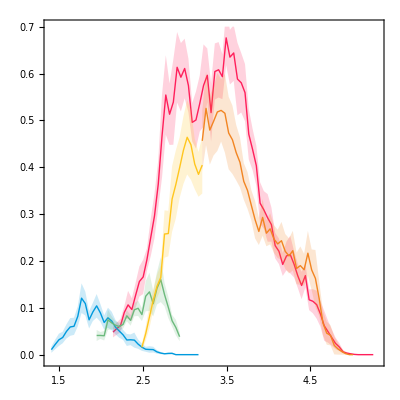

```mathematica
Show[g1,g2,g3,g4,g5]
```

```mathematica
(******************************)
```

```mathematica
totalCellDensitiesPerMouseV1=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/Figure1/Fig1Data/","/",mouseList[[n]],"/",mouseList[[n]],"_RH_V1_TotalCellDensity.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
totalCellDensitiesV1=Flatten[totalCellDensitiesPerMouseV1];
```

```mathematica
(**)
```

```mathematica
totalCellDensitiesPerMouseLP=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/Figure1/Fig1Data/","/",mouseList[[n]],"/",mouseList[[n]],"_RH_LP_TotalCellDensity.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
totalCellDensitiesLP=Flatten[totalCellDensitiesPerMouseLP];
```

```mathematica
(**)
```

```mathematica
totalCellDensitiesPerMouseRL=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/Figure1/Fig1Data/","/",mouseList[[n]],"/",mouseList[[n]],"_RH_RL_TotalCellDensity.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
totalCellDensitiesRL=Flatten[totalCellDensitiesPerMouseRL];
```

```mathematica
(**)
```

```mathematica
totalCellDensitiesPerMouseAL=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/Figure1/Fig1Data/","/",mouseList[[n]],"/",mouseList[[n]],"_RH_AL_TotalCellDensity.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
totalCellDensitiesAL=Flatten[totalCellDensitiesPerMouseAL];
```

```mathematica
(**)
```

```mathematica
totalCellDensitiesPerMouseLM=Table[ToExpression/@Import[StringJoin["F:/FigureGeneration/Figure1/Fig1Data/","/",mouseList[[n]],"/",mouseList[[n]],"_RH_LM_TotalCellDensity.txt"],"List"],{n,1,Length[mouseList]}];
```

```mathematica
totalCellDensitiesLM=Flatten[totalCellDensitiesPerMouseLM];
```

```mathematica
(*************)
```

```mathematica
maxTotCellDens=Round[Max[Join[totalCellDensitiesV1,totalCellDensitiesLP,totalCellDensitiesRL,totalCellDensitiesAL,totalCellDensitiesLM]]];
```

```mathematica
v1Xvals=Table[1+RandomReal[{-0.2,0.2}],{Length[totalCellDensitiesV1]}];
```

```mathematica
lpXvals=Table[2+RandomReal[{-0.2,0.2}],{Length[totalCellDensitiesLP]}];
```

```mathematica
rlXvals=Table[3+RandomReal[{-0.2,0.2}],{Length[totalCellDensitiesRL]}];
```

```mathematica
alXvals=Table[4+RandomReal[{-0.2,0.2}],{Length[totalCellDensitiesAL]}];
```

```mathematica
lmXvals=Table[5+RandomReal[{-0.2,0.2}],{Length[totalCellDensitiesLM]}];
```

```mathematica
(***)
```

```mathematica
v1XYcoordsPerMouse=Partition[Riffle[v1Xvals,Flatten@totalCellDensitiesPerMouseV1],2];
```

```mathematica
lpXYcoordsPerMouse=Partition[Riffle[lpXvals,Flatten@totalCellDensitiesPerMouseLP],2];
```

```mathematica
rlXYcoordsPerMouse=Partition[Riffle[rlXvals,Flatten@totalCellDensitiesPerMouseRL],2];
```

```mathematica
alXYcoordsPerMouse=Partition[Riffle[alXvals,Flatten@totalCellDensitiesPerMouseAL],2];
```

```mathematica
lmXYcoordsPerMouse=Partition[Riffle[lmXvals,Flatten@totalCellDensitiesPerMouseLM],2];
```

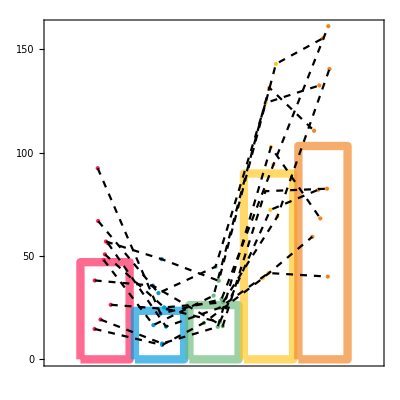

```mathematica
Show[BarChart[{Style[Mean@totalCellDensitiesV1,EdgeForm[{Thickness[0.015],v1Color}]],Style[Mean@totalCellDensitiesLP,EdgeForm[{Thickness[0.015],lpColor}]],Style[Mean@totalCellDensitiesRL,EdgeForm[{Thickness[0.015],rlColor}]],Style[Mean@totalCellDensitiesAL,EdgeForm[{Thickness[0.015],alColor}]],Style[Mean@totalCellDensitiesLM,EdgeForm[{Thickness[0.015],lmColor}]]},ChartStyle->{Transparent,Transparent,Transparent,Transparent,Transparent},FrameTicks->{{LinTicks[0,200,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,PlotRange->{{0,6},{0,maxTotCellDens}}],ListPlot[Partition[Riffle[v1Xvals,totalCellDensitiesV1],2],PlotStyle->Directive[v1Color,PointSize[Large]],FrameTicks->{{LinTicks[0,200,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,PlotRange->{{0,6},{0,maxTotCellDens}}],ListPlot[Partition[Riffle[lpXvals,totalCellDensitiesLP],2],PlotStyle->Directive[lpColor,PointSize[Large]],FrameTicks->{{LinTicks[0,200,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,PlotRange->{{0,6},{0,maxTotCellDens}}],ListPlot[Partition[Riffle[rlXvals,totalCellDensitiesRL],2],PlotStyle->Directive[rlColor,PointSize[Large]],FrameTicks->{{LinTicks[0,200,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,PlotRange->{{0,6},{0,maxTotCellDens}}],ListPlot[Partition[Riffle[alXvals,totalCellDensitiesAL],2],PlotStyle->Directive[alColor,PointSize[Large]],FrameTicks->{{LinTicks[0,200,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,PlotRange->{{0,6},{0,maxTotCellDens}}],ListPlot[Partition[Riffle[lmXvals,totalCellDensitiesLM],2],PlotStyle->Directive[lmColor,PointSize[Large]],FrameTicks->{{LinTicks[0,200,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,PlotRange->{{0,6},{0,maxTotCellDens}}],ListLinePlot[Table[{v1XYcoordsPerMouse[[n]],lpXYcoordsPerMouse[[n]],rlXYcoordsPerMouse[[n]],alXYcoordsPerMouse[[n]],lmXYcoordsPerMouse[[n]]},{n,1,Length[mouseList]}],PlotStyle->Table[{Black,Dashed},{Length[mouseList]}],FrameTicks->{{LinTicks[0,200,MajorTickLength->{0,.03},MinorTickLength->{0,0}],None},{None,None}},Frame->{{True,None},{True,None}},Axes->False,TicksStyle->Thick,FrameStyle->Thick,PlotRange->{{0,6},{0,maxTotCellDens}}],AspectRatio->1, FrameTicksStyle -> Directive[FontOpacity -> 0, FontSize -> 0]]
```